# wbWeinUNICond wbWeinUNINec1Cond

functions that filter the couplings according to the perturbative unitarity conditions of Weinberg's model.

## Documentation

### Usage

wbWeinUNICond[list, M_max ]

Filter the couplings according to the UNI conditions given in Refs. [1, 2]. The couplings are arranged in the following order: list = {a_1, a_2, a_3, b_1, b_2, b_3, c_1, c_2, c_3, d_1, d_2, d_3, ϵ}, with ϵ in radians. The eigenvalues of the scattering matrix are bounded by a quantity M_max, which is typically taken to be 8π. Return: False | True.

wbWeinUNINec1Cond[list, M_max]

This function is identical to wbWeinParRndUni, but includes additional filtering based on the necessary BFB conditions for the 2HDM (NCL1). Return: False | True.

## Examples

To test usage examples make sure the package has been loaded:

```mathematica
wbLoadBinaries=True;(*wpCompTarget="C";*)
NotebookEvaluate[FileNameJoin[{ParentDirectory@NotebookDirectory[EvaluationNotebook[]],"StableWein.nb"}]]
```

### Basic Examples

Generate a set of couplings within the specified range and evaluate the UNI conditions:

```mathematica
couplSet=wbWeinParRndUni[]
```

{1.98604,2.00127,3.95449,8.19476,-7.35215,-0.254506,-5.67433,1.34318,5.12017,4.64439,-6.17459,-1.95678,2.85951}

```mathematica
wbWeinUNICond[couplSet,8 π]
wbWeinUNINec1Cond[couplSet,8 π]
```

True

False

Only a very small fraction of points satisfy the UNI conditions, or both the UNI and necessary BFB conditions, when the parameters are generated within the same ranges:

```mathematica
data=ParallelTable[wbWeinParRnd[16],{10^7}];
dataUNI1=Pick[data,ParallelMap[wbWeinUNICond[#, 8 π]&,data]];
dataUNI2=Pick[data,ParallelMap[wbWeinUNINec1Cond[#, 8 π]&,data]];
Length/@{dataUNI1,dataUNI2}
PercentForm/@N[%/Length[data]]
```

{1234,2}

{0.01234%,0.00002%}

Generating points with function wbWeinParRndUni increases the probability of selecting a point that satisfies the UNI conditions:

```mathematica
data=ParallelTable[wbWeinParRndUni[],{10^7}];
dataUNI1=Pick[data,ParallelMap[wbWeinUNICond[#, 8 π]&,data]];
dataUNI2=Pick[data,ParallelMap[wbWeinUNINec1Cond[#, 8 π]&,data]];
Length/@{dataUNI1,dataUNI2}
PercentForm/@N[%/Length[data]]
```

{40309,110}

{0.4031%,0.0011%}

While function wbWeinParRndUniNec even more increase the probability of selecting a point that satisfies the UNI + NCL1 conditions:

```mathematica
data=ParallelTable[wbWeinParRndUniNec[],{10^7}];
dataUNI1=Pick[data,ParallelMap[wbWeinUNICond[#, 8 π]&,data]];
dataUNI2=Pick[data,ParallelMap[wbWeinUNINec1Cond[#, 8 π]&,data]];
Length/@{dataUNI1,dataUNI2}
PercentForm/@N[%/Length[data]]
```

{70522,2611}

{0.7052%,0.02611%}

### Scope

Couplings generated with appropriate UNI functions:

```mathematica
dataUNI1=ParallelTable[testT=False; While[testT==False,paramT=wbWeinParRndUni[]; testT=wbWeinUNICond[paramT,8 π]]; paramT,{10^6}];
dataUNI2=ParallelTable[testT=False; While[testT==False,paramT=wbWeinParRndUniNec[]; testT=wbWeinUNINec1Cond[paramT,8 π]]; paramT,{10^6}];
```

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUNI1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUNI2),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"wbWeinUNICond[8π]","wbWeinUNINec1Cond[8π]"},{table1,table2}}]);
Grid[{%},Spacings->{4, 0}]
```

wbWeinUNICond[8π]
 | Min | Max
a_1 | -8.37 | 8.37
a_2 | -8.37 | 8.38
a_3 | -8.37 | 8.37
b_1 | -16.19 | 16.34
b_2 | -16.27 | 16.39
b_3 | -16.43 | 16.42
c_1 | -16.64 | 16.7
c_2 | -16.65 | 16.59
c_3 | -16.64 | 16.61
d_1 | -8.37 | 8.37
d_2 | -8.36 | 8.37
d_3 | -8.37 | 8.36
ϵ | 0. | 6.28 | wbWeinUNINec1Cond[8π]
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.38
a_3 | 0. | 8.37
b_1 | -7.63 | 15.51
b_2 | -7.57 | 15.65
b_3 | -7.73 | 15.99
c_1 | -16.04 | 15.84
c_2 | -15.93 | 15.66
c_3 | -16.05 | 15.71
d_1 | -8.09 | 8.16
d_2 | -8.11 | 8.09
d_3 | -8.07 | 8.14
ϵ | 0. | 6.28

Distribution of the couplings filtered with function wbWeinUNICond (green area) and function wbWeinUNINec1Cond with additional necessary BFB conditions for the 2HDM (blue area):

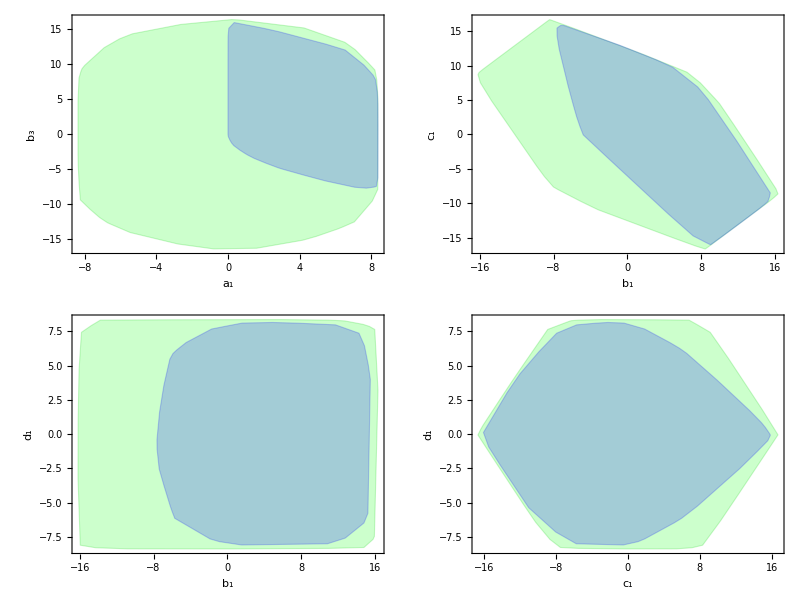

```mathematica
Table[Show[{ConvexHullMesh[dataUNI1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0.2,Green]}],ConvexHullMesh[dataUNI2[[;;,xx]],MeshCellStyle->{1->{Blue},2->Opacity[0.2,Blue]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

### Options

## Source & Additional Information

### Related Symbols

wbWeinParRnd ▪ wbWeinParRndNec ▪ wbWeinParRndUni ▪ wbWeinParRndUniNec ▪ wbWeinSufCond ▪ wbWeinNecCond1 ▪ wbWeinNecCond2 ▪ wbWeinNecCond3 ▪ wbWeinUniBFBcheck

### References

[1] M.P. Bento, J.C. Romao and J.P. Silva, Unitarity bounds for all symmetry-constrained 3HDMs, JHEP 08 (2022), 273, https://doi.org/10.1007/JHEP08(2022)273 [arXiv:2204.13130 [hep-ph]].

[2] S. Moretti and K. Yagyu, Constraints on Parameter Space from Perturbative Unitarity in Models with Three Scalar Doublets, Phys. Rev. D 91 (2015), 055022, https://doi.org/10.1103/PhysRevD.91.055022 [arXiv:1501.06544 [hep-ph]].